```mathematica
fp[x_, y_]:= -x^2(1 + 4y^2/x^2 + Sqrt[1-8y^2/x^2])^(3/2)/(4 Sqrt[2]y(1 + Sqrt[1 - 8y^2/x^2]))
fm[x_, y_]:= -x^2(1 + 4y^2/x^2 - Sqrt[1-8y^2/x^2])^(3/2)/(4 Sqrt[2]y(1 - Sqrt[1 - 8y^2/x^2]))
```

```mathematica
fdiffp[x_, y_, a_]:= fp[x+a/2, y]-fp[x-a/2, y]
fdiffm[x_, y_, a_]:= fm[x+a/2, y]-fm[x-a/2, y]
```

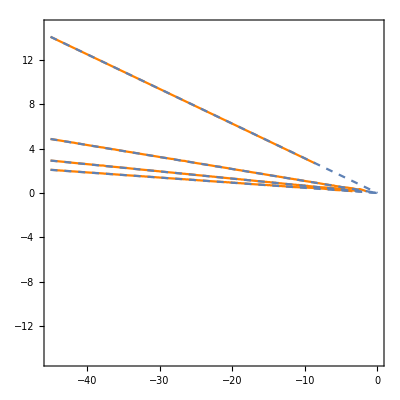

```mathematica
F = 0.7;
a = 1./F^2;
n = Table[i, {i, 0, 3}];
kn = Pi^2 * (2n + 1)^2 * F^4;
slopes = Sqrt[kn-1]/(2kn -1);
Show[
ContourPlot[{fdiffp[x, y, a]==Pi, fdiffp[x, y, a]==3Pi, fdiffp[x, y, a]==5Pi, fdiffp[x, y, a]==7Pi}, {x, -45, 0}, {y, -15, 15}, ContourStyle->Orange],
Plot[-slopes*(x), {x, -45, 0}, PlotRange->{-15, 15}, PlotStyle->Dashed]]
```